# Основы статистики

## Конспект курса со Stepik от Bioinformatics Institute

Александр Нехаев

Введение

## Понятия генеральной совокупности и выборки, репрезентативность выборки

### Понятие выборки и генеральной совокупности

Генеральная совокупность - множество всех объектов относительно которой мы хотим делать выводы в рамках исследования некоторой проблемы

Выборка - часть генеральной совокупности используемой в реальном исследовании.

Репрезентативность выборки - применимость выводов по выборке к генеральной совокупности.

### Выборка

#### Простая случайная выборка (simple random sample)

Случайный выбор элементов из генеральной совокупности.

#### Стратицированная выборка (stratified sample)

Разбиение генеральной совокупности на несколько групп с явно различными свойствами. Затем случайной выборкой берем элементы из каждой группы.

#### Групповая выборка (cluster sample)

Так же разбиваем совокупность на кластеры, которые схожи по свойствам. Затем выбираем несколько кластеров, затем из кластеров выбираем случайные элементы.

## Типы переменных. Количественные и номинативные переменные

### Типы переменных

Все переменные характеризующие генеральные совокупности можно разделить на количественные и номинативные.

#### Количественные переменные

Непрерывные

Дискретные

Например: Непрерывная - рост человека из выборки на интервале от 160 до 190 см. Дискретная - количество детей в семье.

#### Номинативные

Используются для разделения элементов выборки на какие-то группы.

#### Ранговые переменные

Переменная к которой можно применять только операцию сравнения.

## Меры центральной тенденции

### Понятие описательной статистики

Гистограмма частот - первое описание формы распределения.

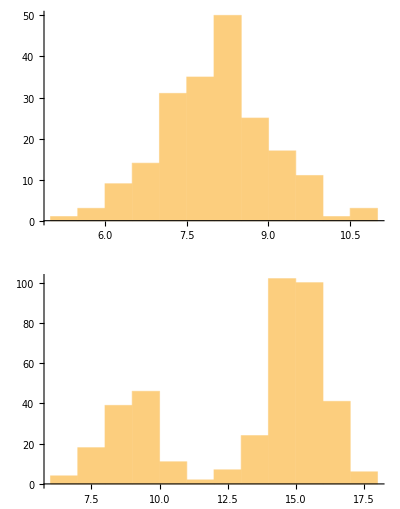

```mathematica
GraphicsGrid[{{
Histogram[RandomVariate[NormalDistribution[8,1],200]]},{
Histogram[RandomVariate[
MixtureDistribution[{1,2},{NormalDistribution[9,1],NormalDistribution[15,1]}],
400]]
}}]
```

#### Мера центральной тенденции

Отвечает на вопрос насколько высокие значения принимает переменная.

### Мода

Мода - значение измеряемого признака, которое встречается максимально часто.

Пример: Пусть есть выборка:

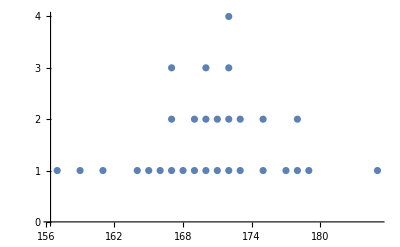

```mathematica
a={185,175,170,169,171,172,175,157,170,172,167,173,168,167,166,167,169,172,177,178,165,161,179,159,164,178,172,170,173,171};
DotPlot[data_]:=Module[{m=Tally[Sort[data]]},ListPlot[Flatten[Table[{#1,n},{n,#2}]&@@@m,1],Ticks->{Automatic,Range[0,Max[m[[All,2]]]]}]];
DotPlot[a]
```

```mathematica
Commonest[a]
```

{172}

### Медиана

Медиана - значение признака, которое делит упорядоченное множество данных пополам

```mathematica
b={157,159,161,164,165,166,167,167,167};
```

```mathematica
Length@b
```

9

```mathematica
Median[b]
```

165

В случае если у нас нечетное количество элементов - все просто. Если нечетное, то берем среднее значение двух значений между которыми находится середина.

```mathematica
a
```

{185,175,170,169,171,172,175,157,170,172,167,173,168,167,166,167,169,172,177,178,165,161,179,159,164,178,172,170,173,171}

```mathematica
Median@a//N
```

170.5

### Среднее значение

Среднее значение - сумма всех значений измеренного признака, деленная на количество измеренных значений.

```mathematica
Mean@a//N
```

170.4

### Выбор меры центральной тенденции

Смотрим на все значения, которые мы получили:

```mathematica
{ToString/@#,Flatten@Through[#[a]]}&@{Commonest,Median,Mean}ᵀ//TableForm
```

Commonest | 172
Median | 341/2
Mean | 852/5

Если распределение симметрично, унимодально и не имеет заметных выбросов, то все тенденции дадут примерно одно значение. Если оно ассиметрично, с выбросами или мультмодально, тогда лучше использовать моду или медиану.

### Свойства среднего

M_(x+c)=M_x+c

M_(x*c)=M_x*c

∑(x_i-M_x)=0 (видимо только для целочисленных выборок)

```mathematica
Through[{
(Mean[#+2]==Mean[#]+2)&,
(Mean[#*2]==Mean[#]*2)&,
Total[#-Mean[#]]==0&
}[Round@RandomVariate[NormalDistribution[],200]]]
```

{True,True,True}

## Меры изменчивости

### Понятие меры изменчивости данных

Некоторые распределения имеют значительные отличия в виде даже несмотря на близкие значения среднего, медианы и моды. Для описания их отличий используются меры изменчивости.

### Размах

Размах разность - максимального и минимального значений.

```mathematica
DotPlot[a]
```

-Graphics-

```mathematica
Subtract@@Reverse@MinMax[a]
```

28

Изменение краевых величин будет сильно влиять на эту меру.

### Дисперсия, стандартное отклонение

Дисперсия - средний квадрат отклонений индивидуальных значений признака от их средней величины.

Среднее отклонение от среднего вообще говоря имеет вид:

(∑(x_i-x̄))/n

Но как мы знаем их свойств среднего, числитель тогда будет равен 0. Исключаем отрицательные значения через возведение в квадрат:

(∑(x_i-x̄)^2)/n

Это и называется дисперсией.

```mathematica
Variance@a//N
```

36.0414

Однако мы взяли квадрат, что сильно влияет на результат (можно сказать, что поменялась размерность). Поэтому более точной величиной будет корень из нее.

Стандартное отклонение - корень из дисперсии.

```mathematica
StandardDeviation@a//N
```

6.00345

Тут стоит отметить, что в литературе для обозначения стандартного отклонения для всей генеральной совокупности используется символ σ. Для стандартного отклонения выборки используется sd.

Еще момент. Если мы считаем дисперсию для всей генеральной совокупности, то мы смело используем формулу (0.1). Однако если мы берем дисперсию для совокупности, то в знаменателе используем n-1. Это связано со степенями свободы.

#### Пример

```mathematica
c={1,2,2,3,4,4,5};
Mean@c
```

3

```mathematica
(c-Mean@c)^2
```

{4,1,1,0,1,1,4}

```mathematica
(*D*)Total[(c-Mean@c)^2]/(Length@c-1)
```

2

```mathematica
(*sd*) √(Total[(c-Mean@c)^2]/(Length@c-1))//N
```

1.41421

На встроенных функциях то же самое:

```mathematica
Variance@c
StandardDeviation@c//N
```

2

1.41421

### Свойства диспресии и стандарнтного отклонения

D_(x+c)=D_x

sd_(x+c)=sd_x

D_(x*c)=D_x*c^2

sd_(x*c)=sd_x+c

## Квартили распределения и график box-plot

### Квантили распределения

Квантили - это такие значения признака, которые делят упорядоченные данные на некоторое число равных частей.

Примером квартиля является медиана, которую мы уже рассматривали, однако в статистике так же часто используются квартили распределения - 3 точки, которые делят распределение на 4 равных части.

### Квартили

Квартили - три точки (значения признака), которые делят упорядоченное множество данных на 4 равные части.

```mathematica
Sort@a
```

{157,159,161,164,165,166,167,167,167,168,169,169,170,170,170,171,171,172,172,172,172,173,173,175,175,177,178,178,179,185}

```mathematica
Quartiles[a]
```

{167,341/2,173}

### Box-plot

Верхняя и нижняя границы коробки отражают положение 1го и 3го квартилей. Линия внутри коробки - 2й квартиль (медиана). Положения усов - последние значения в пределе 1.5 межквартильных размахов от границ коробки. Точки - выпадающие из них значения.

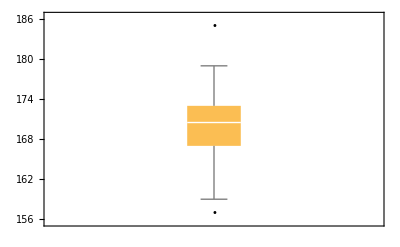

```mathematica
BoxWhiskerChart[a,"Outliers"]
```

Теперь нанесем точки на график с box-plot:

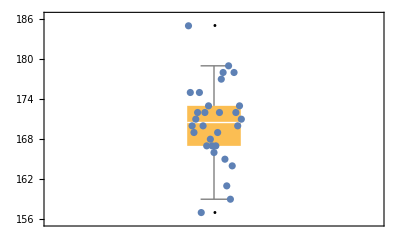

```mathematica
Show[
BoxWhiskerChart[a,"Outliers"],
ListPlot[{0.8+0.4(Table[i, {i, 1, Length@a}]/Length@a), a}ᵀ]
]
```

Box plot не столь информативен, сколько гистограмма, однако он помогает при сравнении двух распределений.

## Нормальное распределение

### Понятие нормального распределения

Характеристики:

Унимодально

Симметрично

Отклонение наблюдений от среднего подчиняется определенному вероятностному закону:

В диапазоне от медианы до среднеквадратичного отклонения будет находиться примерно 34.1% всех значений.

В диапазоне от одного до двух среднеквадратичных отклонений будет находиться примерно 13.6%.

Вероятность встретить значение, превосходящее 3 стандартных отклонения весьма маловероятна (там около 0.1% значений).

### Стандартизация

Стандартизация или z-преобразование – преобразование полученных данных в стандартную Z-шкалу (Z-scores) со средним M_z=0 и D_z=1.

Для этого:

Z_i=(x_i-x̄)/σ_x

Видим, что форма распределения не меняется, меняются только значения:

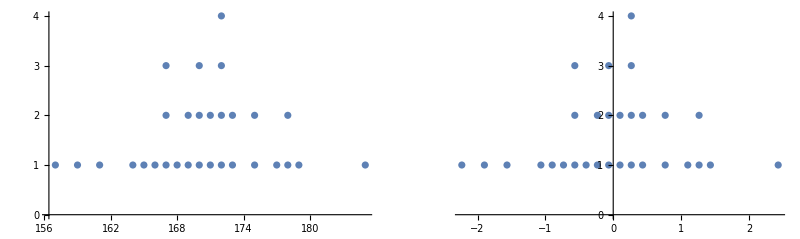

```mathematica
GraphicsGrid[{{DotPlot@a,DotPlot@Standardize[a]}}]
```

### Правила двух и трех сигм, использование стандартизации

Ранее уже говорили, что:

M_x±σ≈68% наблюдений

M_x±2σ≈95% наблюдений

M_x±3σ≈100% наблюдений

z-преобразование позволяет ответить на вопрос какой процент наблюдений лежит в любом заданном диапазоне.

Пример: Мы хотим узнать какой процент значений превышает значение 154 если среднее значение составляет 150, а стандартное отклонение равно 8.

Находим z-значение для заданного значения:

```mathematica
z=(154-150)/8
```

1/2

```mathematica
Probability[x>z,x\[Distributed]NormalDistribution[0,1]]//N
```

0.308538

## Центральная предельная теорема

Допустим, что некоторый признак распределен нормально в генеральной совокупности имеет среднее значение и стандартное отклонение:

```mathematica
μ=0;
σ=15;
```

Обозначаем эту совокупность

```mathematica
dist=Round[RandomVariate[NormalDistribution[μ,σ],175*5000]];
```

и строим её:

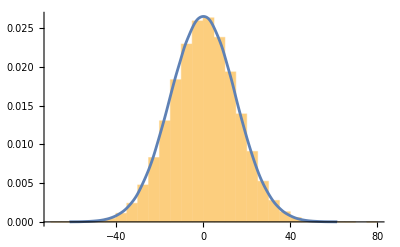

```mathematica
Show[
Histogram[dist, Automatic, "PDF"],
SmoothHistogram[dist,Automatic,"PDF"]
]
```

Будем многократно извлекать из совокупности выборки по 175 значений каждая и замерять в них среднее значение и стандартное отклонение (отображены первые 8 выборок):

```mathematica
sampleSize=175;
```

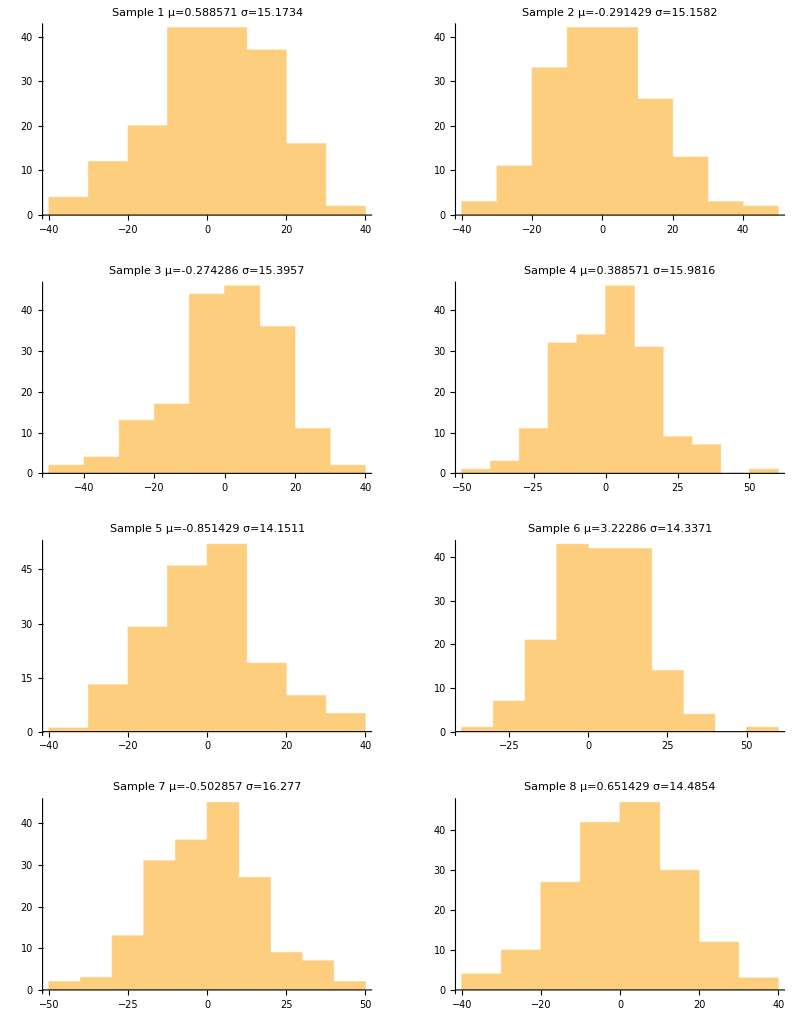

```mathematica
samples=Table[RandomChoice[dist, sampleSize],{i,0,Length[dist]/sampleSize}];
Graphics[Histogram[#,PlotLabel->"Sample "<>ToString[Position[samples,#][[1,1]]]<>" μ="<>ToString@N[Mean[#]]<> " σ="<>ToString@N[StandardDeviation[#]]
]
]&/@samples[[1;;8]]//GraphicsGrid[ArrayReshape[{#},{4,2}]]&
```

Теперь возьмем рассчитанные значения среднего и стандартного отклонения для всех выборок и отобразим их на графике:

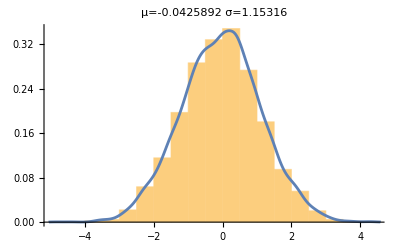

```mathematica
samplesData=Through[{Mean,StandardDeviation}[#]]&/@samples;
Show[
Histogram[samplesData[[All,1]], Automatic, "PDF",PlotLabel->"μ="<>ToString[N@Mean[samplesData[[All,1]]]]<>" σ="<>ToString[N@StandardDeviation[samplesData[[All,1]]]]
],
SmoothHistogram[samplesData[[All,1]],Automatic,"PDF"]
]
```

Значение σ на этом графике называется стандартной ошибкой среднего и показывает на сколько в среднем значение выборочного значения среднего отклоняется от среднего генеральной совокупности. С ростом количества элементов в выборке стандартная ошибка среднего будет уменьшаться.

Таким образом формулируем центральную предельную теорему.

Предположим исследуемый признак имеет нормальное распределение в генеральной совокупности с некоторым средним значением и стандартным отклонением и мы многократно извлекаем выборки равные по объему n и в каждой выборке рассчитываем среднее значение после чего строим распределение средних значений. Такое распределение будет являться нормальным со средним, совпадающем со среднем генеральной совокупности и со стандартным отклонением, называемым стандартной ошибкой среднего и рассчитываемым по формуле:

se=σ/(√n)

Замечание: на самом деле исследуемый признак может иметь любое распределение и средние выборок так же будут распределены нормально.

Чем больше элементов в выборке, тем ближе среднее значение в каждой выборке к среднему значению генеральной совокупности и соответственно тем меньше будет стандартная ошибка среднего.

Так же есть правило, что если число элементов в выборке больше 30 и эта выборка репрезентативная, то формулу из теоремы можно преобразовать до вида:

se=(sd x)/(√n).

Пусть мы извлекли из совокупности всего одну выборку в 100 элементов. Стандартное отклонение 5 и среднее значение 3. На основе этих данных мы можем предположить, как вели бы себя все выборки этой совокупности:

```mathematica
5/(√100)
```

1/2

Соответственно распределение средних значений выборок имело бы вид:

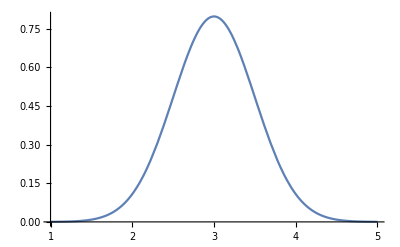

```mathematica
Plot[PDF[NormalDistribution[3,5/(√100)],x],{x,1,5}]
```

Утверждается, что данное распределение будет получатся во всех выборках.

## Доверительные интервалы для среднего

Одна из задач в которых можно использовать ЦПТ - построение доверительного интервала. Рассмотрим задачу.

Уровень экспрессии некоторого гена измерялся в эксперименте. Ниже представлены результаты 64 наблюдений.

```mathematica
sample={102,91,99,100,103,98,99,101,106,88,103,97,103,101,101,91,104,105,105,100,101,91,99,98,107,102,100,97,98,104,100,98,102,99,95,103,104,97,99,102,98,107,101,93,98,101,93,91,107,102,96,93,100,105,103,107,99,102,106,102,94,104,103,102};
```

Чему равен показатель экспрессии этого гена во всей генеральной совокупности.

Сразу оговорим, что мы не можем рассчитать точное значение экспрессии для генеральной совокупности, однако мы можем посчитать интервал, в котором оно будет лежать.

Вспоминаем ЦПТ. Мы знаем, что если бы мы многократно повторяли наш эксперимент, то все выборочные средние распределились бы нормальным образом вокруг среднего генеральной совокупности (которую мы и ищем) со стандартной ошибкой среднего se=sd_x/(√n). Так же мы знаем, что 95% всех выборочных средних лежали бы в диапазоне ±1.96se. Но при этом мы не знаем чему равняется среднее генеральной совокупности и насколько сильно от него отклонилось выборочное среднее.

Однако взглянем на это с другой стороны. Пусть мы рассчитываем показатель OverBar[x_i]±1.96se для каждого выборочного среднего, то этот интервал будет включать в себя среднее всей генеральной совокупности. Это будет справделиво для 95% средних из генеральной совокупности. Не попадают под это правило только те выборочные средние, которые расположены очень далеко.

Теперь расчитываем.

Значения среднего и стандартного отклонения:

```mathematica
x̄=Mean@sample
sd=N@StandardDeviation@sample
n=Length@sample
```

100

4.45079

64

Теперь считаем значение стандартной ошибки:

```mathematica
se=sd/(√n)
```

0.556349

Теперь считаем 95% доверительный интервал:

```mathematica
Around[x̄,1.96se]
```

100.01.1

То есть:

```mathematica
{#[[1]]-#[[2]],#[[1]]+#[[2]]}&@Around[x̄,1.96se]
```

{98.9096,101.09}

Мы можем расширить степень нашей уверенности - найти более широкий доверительный интервал. Если для 95% мы использовали выражение μ±1.96σ, то для 99% мы можем использовать выражение μ±2.58σ. и тогда интервал будет иметь вид:

```mathematica
{#[[1]]-#[[2]],#[[1]]+#[[2]]}&@Around[x̄,2.58se]
```

{98.5646,101.435}

## Идея статистического вывода, p-уровень значимости

### Статистическая проверка гипотез

Как правило нас все таки интересуют гипотезы, а не конкретные значения.

Рассмотрим пример:

Предположим, что на выздоровление при некотором заболевании в среднем требуется M=20 дней, но мы разработали новый препарат и хотим проверить может ли он сократить этот срок. Мы взяли 64 пациента и опробовали на них новый метод лечения. Оказалось, что средняя скорость выздоровления сократилась до x̄=18.5 дней при среднем стандартном отклонении sd=4. Какой вывод можно сделать из этих данных?

С одной стороны судя по значениям, мы действительно сократили срок выздоровления. С другой стороны, такой результат мог быть получен случайно и без препарата. Введем несколько важных понятий.

В этом исследовании будут конкурировать 2 гипотезы:

H_0 - никакого реального воздействия препарат не оказывает и на самом деле среднее значение генеральной совокупности тех пациентов, которые получили препарат на самом деле не отличается от генеральной совокупности всех больных, M_НП=20.

H_1 - препарат влияет и среднее значение скорости восстановления генеральной совокупности всех пациентов, использующих препарат отличается, M_НП≠20.

Пусть на самом деле верна первая гипотеза. Тогда согласно ЦПТ если бы мы многократно повторяли исследование, то выборочные средние распределились бы нормальным образом вокруг среднего генеральной совокупности с стандартной ошибкой se=sd/(√n)=4/(√64)=0.5. Теперь ответим на вопрос “насколько далеко наше выборочное среднее отклонилось от предполагаемого среднего значения генеральной совокупности в единицах стандартного отклонения?” Для этого делаем z-преобразование:

z=(x̄-M)/se=(18.5-20)/0.5=-3

Это означает, что если бы в генеральной совокупности среднее значение на самом деле равнялось бы 20, то выборочно среднее отклонилось бы от среднего генеральной совокупности на -3σ влево.

### Идея статистического вывода

Теперь воспользуемся свойствами нормального распределения чтобы рассчитать вероятность такого или еще более сильно выраженного отклонения от среднего значения:

```mathematica
N@Probability[x<-3||x>3,x\[Distributed]NormalDistribution[0,1]]
```

0.0026998

Итак, на первом этапе мы предположили, что на самом деле верна нулевая гипотеза. Если это так, то все выборочные средние распределились бы вокруг среднего генеральной совокупности, которое, как мы предполагаем, равняется 20. Однако в нашем эксперименте выборочное среднее оказалось равно 18.5. Зная стандартную ошибку среднего мы смогли рассчитать вероятность получить такое или еще более сильно выраженное отклонение причем как в правую, так и в левую сторону. Оказалось, что такая вероятность ≈0.003.

Таким образом основная идея статистического вывода заключается в следующем: мы допускам, что верна нулевая гипотеза и на самом деле никаких различий у нас нет. Затем мы считаем вероятность того, что мы получили такие или еще более сильно выраженные различия абсолютно случайно. Это значение в статистике называется p-уровень значимости и именно при помощи этого показателя мы выясним какую гипотезу считать более состоятельной. Чем меньше p-уровень, тем больше оснований отклонить нулевую гипотезу. Считается, что если p<0.05, то можно смело принимать альтернативную гипотезу. Однако если p-уровень больше этого порога, у нас недостаточно оснований отклонить эту гипотезу.

### p-уровень значимости и его интерпретация

Получаем, что у нас достаточно оснований для отклонения нулевой гипотезы. Вопрос - зачем рассчитывать значение отклонения в принципиально другом направлении? Ведь если мы проверили гипотезу о том, что препарат ускорит скорость выздоровления, то зачем учитывать вероятность, что он её понизит? Вероятность это площадь под кривой. Если рассматривать только одно направление, то вероятность события будет меньше. Тем не менее принято учитывать оба конца распределения. Реально мы не знаем в какую сторону мы получим отклонение от среднего и от такого развития событий никто не застрахован. Иногда действительно используется односторонний p-критерий, обычно если отклонение в другую сторону невозможно.

В реальности p-уровень означает, что если верна нулевая гипотеза, то вероятность получить такие или еще более выраженные различия будет равна p-уровню. Он ничего не говорит о силе эффекта. Мы можем получить в среднем сокращение времени болезни на неделю, но при этом не значимое с точки зрения статистики.

Что делать, если уровень значимости оказался больше 0.05? Вывод простой - у нас недостаточно оснований для отклонения нулевой гипотезы. Сам по себе p-уровень ничего не говорит ни о правильности, ни о ценности получаемых результатов.

Основная идея статистической проверки гипотезы подразумевает, что мы иногда будем совершать статистические ошибки 1го и 2го рода.

Ошибка 1го рода подразумевает, что мы отклонили первую гипотезу, хотя на самом деле она верна.

Ошибка 2го рода подразумевает, что мы не отклонили нулевую гипотезу, хотя на самом деле она не верна.

Сравнение средних

## T-распределение

### Нормальное распределение и ограниченность количества наблюдений

С выборками в которых большое число элементов все понятно. Теперь рассмотрим ситуацию, когда число элементов достаточно мало (<30). Особенность такого случая заключается в том, что нарушается предположение о том, что во-первых, стандартное отклонение среднего уже не такое хорошее, а во-вторых нарушается предположение о том, что все выборочные средние будут вести себя в соответствии с нормальным распределением.

### Распределение Стьюдента (T-распределение)

По этим причинам, если число наблюдений невелико и стандартное отклонение неизвестно, то используется распределение Стьюдента (t-распределение).

Распределение Стьюдента унимодально и симметрично, но наблюдения с большой вероятностью попадают за пределы ±2σ от M.

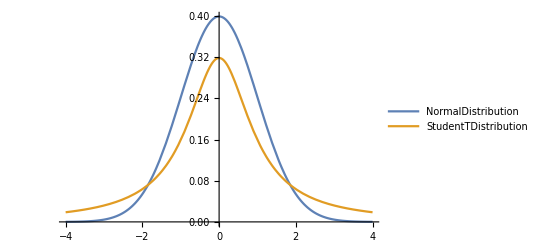

```mathematica
Plot[{PDF[NormalDistribution[0,1],x],PDF[StudentTDistribution[1],x]},{x,-4,4},PlotLegends->{NormalDistribution,StudentTDistribution}]
```

Форма распределения определяется числом степеней свободы (df=n-1), где n - число наблюдений в выборке. С увеличением число df распределение стремится к нормальном.

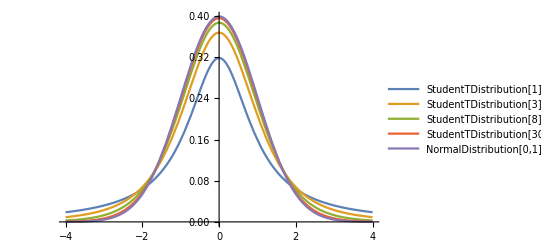

```mathematica
df={1,3,8,30};
tdists=StudentTDistribution/@df;
dists=Append[tdists,NormalDistribution[0,1]];
pdfs=PDF[#,x]&/@dists;
tStudentDemoPlot=Plot[pdfs,{x,-4,4},PlotLegends->dists]
```

Рассмотрим пример. Пусть в генеральной совокупности среднее значение μ=10. На выборке получили среднее равное x̄=10.8 со стандартным отклонением sd=2 при числе испытаний N=25.

Если пользоваться стандартной формулой описанной ранее, то мы бы сказали, что в соответствии с ЦПТ все выборочные средние распределились бы нормально вокруг среднего генеральной совокупности и стандартная ошибка среднего была бы:

```mathematica
se=2/(√25)//N
```

0.4

Теперь мы хотим посмотреть насколько наше выборочное среднее отклонилось от среднего генеральной совокупности. Тогда мы сможем найти вероятность получить такое или еще более выраженное отклонение. Для этого ищем соответствующее z-значение:

```mathematica
z=(10.8-10)/0.4
```

2.

То есть отклонение составляет 2 стандартных отклонения. Теперь найдем вероятность такого или большего отклонения.

Теперь чуть больше поговорим о том, почему t-распределение необходимо на небольшом объеме выборки.

Про необходимость t-критерия

Мы знаем, что если некоторый признак в генеральной совокупности распределен нормально (или согласно какому-либо другому распределению) со средним μ и стандартным отклонением σ и мы будем многократно извлекать выборки одинакового размера n, и для каждой выборки рассчитывать, как далеко выборочное среднее X̄ отклонилось от среднего в генеральной совокупности в единицах стандартной ошибки среднего:

z=(X̄-μ)/(σ/(√n))

то эта величина z будет иметь стандартное нормальное распределение со средним равным нулю и стандартным отклонением равным единице.

Обратим внимание, что для расчета стандартной ошибки мы используем именно стандартное отклонение в генеральной совокупности - σ. Ранее мы уже обсуждали, что на практике σ нам практически никогда не известна, и для расчетов стандартной ошибки мы используем выборочное стандартное отклонение.

Строго говоря в таком случае распределение отклонения выборочного среднего и среднего в генеральной совокупности, деленного на стандартную ошибку, теперь будет описываться именно при помощи t-распределения.

t=(X̄-μ)/(sd/(√n))

Таким образом, в случае неизвестной σ мы всегда будем иметь дело с t-распределением. На этом этапе возникает вопрос, почему в предыдущей главе использовался z-критерий для проверки гипотез, используя выборочное стандартное отклонение?

Мы уже знаем, что при довольно большом объеме выборки (n>30) t-распределение совсем близко подбирается к нормальному распределению:

```mathematica
tStudentDemoPlot
```

-Graphics-

Поэтому иногда для простоты расчетов говорится, что если n>30, то мы будем использовать свойства нормального распределения для наших целей. Строго говоря, это конечно неправильный подход, который часто критикуют. В до компьютерную эпоху этому было некоторое объяснение, чтобы не рассчитывать для каждого n большего 30 соответствующее критическое значение t-распределения, статистики как бы округляли результат и использовали нормальное распределение для этих целей. Сегодня с этим больше проблем нет и все статистические программы без труда рассчитывают все необходимые показатели для t-распределения с любым числом степеней свободы. Действительно при выборках очень большого объема t-распределение практически не будет отличаться от нормального, однако хоть и очень малые различия все равно будут.

Поэтому, правильнее будет сказать, что мы используем t-распределение не потому что у нас маленькие выборки, а потому что мы не знаем стандартное отклонение в генеральной совокупности. Поэтому в дальнейшем мы всегда будем использовать t-распределение для проверки гипотез, если нам неизвестно стандартное отклонение в генеральной совокупности, необходимое для расчета стандартной ошибки, даже если объем выборки больше 30.

Если мы допустили, что все выборочные средние будут распределены нормальным образом, то вероятность получить отклонение превышающее 2σ как в левую, так и в правую сторону будет составлять:

```mathematica
N@Probability[x<-z||x>z,x\[Distributed]NormalDistribution[0,1]]
```

0.0455003

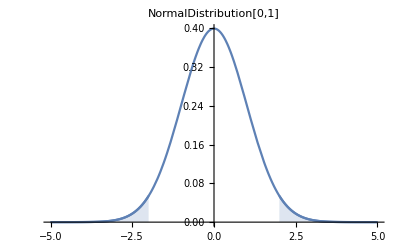

```mathematica
Show[Plot[PDF[#,x],{x,-5,5},PlotLabel->#],
Plot[PDF[#,x],{x,-5,-z},Filling->Axis,PlotRange->All],
Plot[PDF[#,x],{x,z,5},Filling->Axis,PlotRange->All]
]&@NormalDistribution[0,1]
```

То есть p-уровень значимости будет меньше чем 0.05 и мы смело сможем отклонить нулевую гипотезу, согласно которой наша выборка принадлежит генеральной совокупности со среднем значением 10.8. Но как мы сказали при небольшом объеме выборки распределение выборочного среднего будет отличаться от нормального и вероятность получить более выраженное отклонение от среднего станет выше. Рассчитаем данную вероятность предположив, что мы работаем с t-распределением с 24 степенями свободы.

```mathematica
N@Probability[x<-z||x>z,x\[Distributed]StudentTDistribution[25-1]]
```

0.0569398

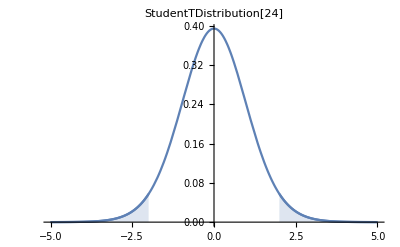

```mathematica
Show[Plot[PDF[#,x],{x,-5,5},PlotLabel->#],
Plot[PDF[#,x],{x,-5,-z},Filling->Axis,PlotRange->All],
Plot[PDF[#,x],{x,z,5},Filling->Axis,PlotRange->All]
]&@StudentTDistribution[25-1]
```

Это означает, что если бы мы пользовались t-распределением, то нулевую гипотезу мы бы отклонить не смогли.

t-критерий рассчитывается так же как z-критерий:

t=(x̄-M)/(sd/(√n))

Однако если бы мы в этом случае получили 2, то в t-распределении с 24 степенями свободы p=0.056 и нулевую гипотезу мы бы отклонить не смогли.

### Понятие числа степеней свободы

Как уже понятно t-распределение зависит от числа наблюдений в выборке как n-1. Если дать более общее определение, то число степеней свободы - это число элементов которые могут варьироваться при расчете некоторого статистического показателя.

## Сравнение двух средних, t-критерий Стьюдента

### Сравнение двух средних

Критерий который позволяет сравнивать между собой два выборочных средних называется парным t-тестом или просто t-критерием Стьюдента.

### t-критерий Стьюдента

Предположим мы хотим сравнить два средних выборочных значения OverBar[x_1] рассчитанное на выборке со стандартным отклонением sd_1 и числом элементов выборки n_1 и OverBar[x_2] с sd_2 и n_2. Сначала сформулируем статистические гипотезы:

H_0 - в генеральной совокупности никакого различия между этими значениями нет и μ_1=μ_2.

H_1 - μ_1≠μ_2.

Предположим, что верна нулевая гипотеза. Если это так, то при многократном повторении эксперимента и каждый раз рассчитывали разность между двумя выборочными средними значениями OverBar[x_1]-OverBar[x_2], то эта величина распределилась бы следующим образом: мы бы получили симметричное распределение с средним значением μ_1-μ_2=0 и стандартной ошибкой se=√(sd_1^2/n_1+sd_2^2/n_2). Причем это распределение будет t-распределением с числом степеней свобод, вычисляемым по формуле df=n_1+n_2-2. На основе этой информации мы можем рассчитать насколько далеко конкретно наша разность между двумя средними значениями отклонилась от предполагаемого показателя генеральной совокупности и тем самым рассчитать вероятность получить такие или еще более сильные отклонения при условии, что на самом деле нулевая гипотеза верна.

Окончательная формула для t-критерия будет иметь вид:

t=((OverBar[x_1]-OverBar[x_2])-(μ_1-μ_2))/(√(sd_1^2/n_1+sd_2^2/n_2))

На основе этого показателя и зная число степеней свобод (df=n_1+n_2-2) мы можем рассчитать p-уровень значимости, который покажет нам вероятность получить такое или еще более выраженное отклонение при условии, что нулевая гипотеза верна.

Пример: Процесс денатурации ДНК представляет разрушение водородных связей между двумя цепями этой молекулы и очень сильно зависит от температуры, с которой мы воздействуем на молекулу.

```mathematica
spec1={84.7,105.0,98.9,97.9,108.7,81.3,99.4,89.4,93.0,119.3,99.2,99.4,97.1,112.4,99.8,94.7,114.0,95.1,115.5,111.5};
spec2={57.2,68.6,104.4,95.1,89.9,70.8,83.5,60.1,75.7,102.0,69.0,79.6,68.9,98.6,76.0,74.8,56.0,55.6,69.4,59.5};
ds=Dataset[<|1->spec1,2->spec2|>]
```

При сравнении двух видов между собой были получены следующие различия в средней температуре плавления ДНК:

```mathematica
dsStats=ds[All,<|"M"->Mean,"SD"->StandardDeviation,"N"->Length|>]
```

Формулируем гипотезы:

H_0: μ_1=μ_2

H_1: μ_1≠μ_2

Считаем t-критерий:

```mathematica
t=(dsStats[1]["M"]-dsStats[2]["M"])/(√((dsStats[1]["SD"])^2/(dsStats[1]["N"])+(dsStats[2]["SD"])^2/(dsStats[2]["N"])))
```

6.04782

Число степеней свобод:

```mathematica
df=dsStats[1]["N"]+dsStats[2]["N"]-2
```

38

Считаем интересующую нас вероятность:

```mathematica
p=Probability[x<-t||x>t,x\[Distributed]StudentTDistribution[df]]
```

4.8947×10^-7

Программно можно сильно проще:

```mathematica
TTest[Normal@Values@ds]
```

4.8947×10^-7

Это меньше чем пороговое значение для p:

```mathematica
p<0.05
```

True

Таким образом мы обнаружили статистически значимое различие в средней температуре плавления ДНК двух видов.

### Построение графиков

Для начала как делать не надо (что это вообще такое?):

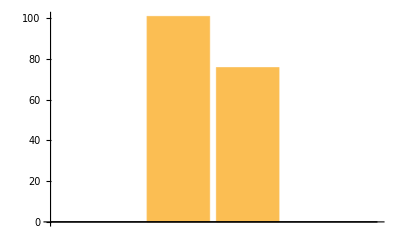

```mathematica
BarChart@Values@Normal@dsStats[All,"M"]
```

Как лучше:

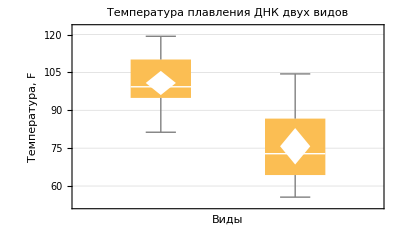

```mathematica
BoxWhiskerChart[ds,{{"MeanDiamond"},{"Outliers"}},PlotLabel->"Температура плавления ДНК двух видов",FrameLabel->{"Виды","Температура, F"},PlotTheme->"Detailed"]
```

## Проверка распределений на нормальность, QQ-Plot

### Сравнение распределения с нормальным

Требование к нормальному распределению очень часто встречается в статистике при использовании различных методов. Как оценить отличие распределения от нормального?

Один из самых простых способов - построить гистограмму частот признака и поверх наложить кривую идеального нормального распределения. Например:

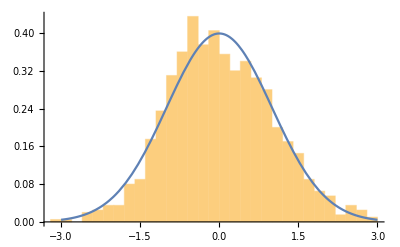

```mathematica
dist=RandomVariate[NormalDistribution[0,1],1000];
Show[
Histogram[dist,Automatic,"PDF"],
Plot[PDF[NormalDistribution[0,1],x],{x,-3,3}]
]
```

### QQ-plot

Еще один графический способ проверить распределение на нормальность - QQ-plot

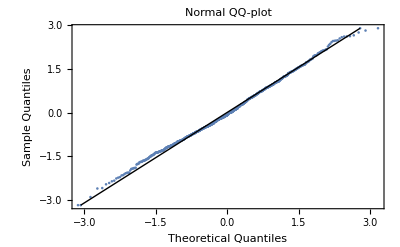

```mathematica
QuantilePlot[
dist,
FrameLabel->{"Theoretical Quantiles","Sample Quantiles"},
PlotLabel->"Normal QQ-plot"
]
```

QQ-plot удобно использовать, когда число наблюдений невелико. Данных для построения гистограммы мало и удобно анализировать каждое значение отдельно что и возможно по такому графику.

Попробуем проверить этот метод на задаче с температурой плавление ДНК у видов.

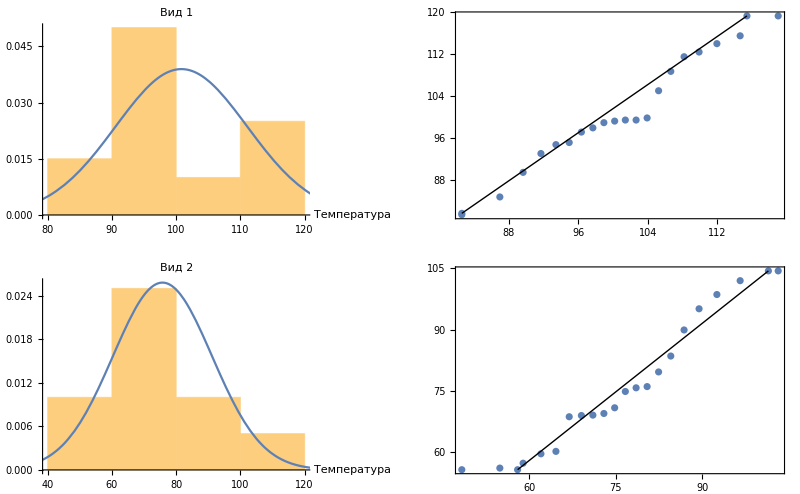

```mathematica
{Show[Histogram[#,Automatic,"PDF",AxesLabel->{"Температура"},PlotLabel->"Вид "<>ToString@PositionIndex[Normal@ds][#][[1]]],Plot[PDF[NormalDistribution[Mean[#],StandardDeviation[#]],x],{x,Mean[#]-3StandardDeviation[#],Mean[#]+3StandardDeviation[#]}]],
QuantilePlot[#]
}&/@{spec1,spec2}//GraphicsGrid
```

### Тест Шапиро-Вилка

Тест Шапиро-Вилка позволяет определить что выборка изъята из генеральной совокупности и её распределение соотвествует нормальному.

```mathematica
ds[All,<|"SWT"->ShapiroWilkTest|>]
```

Если уровень SWT > 0.05 это хорошо и не позволяет отклонить нулевую гипотезу.

### Проблема выбросов

Посмотрим как влияет появление выбросов на параметры выборки. Для этого добавим по одному выбросу в каждый из наборов значений в задаче про температуру плавления и сравним результаты со старыми.

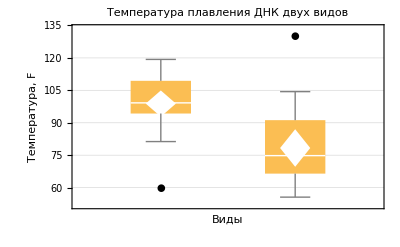

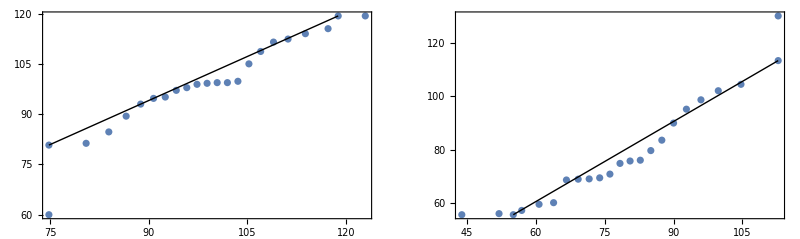

```mathematica
dsDamaged=Dataset@<|1->#1,2->#2|>&@@Transpose@Append[Normal@Values[ds]ᵀ,{60,130}]
BoxWhiskerChart[dsDamaged,{{"MeanDiamond"},{"Outliers"}},PlotLabel->"Температура плавления ДНК двух видов",FrameLabel->{"Виды","Температура, F"},PlotTheme->"Detailed"]
QuantilePlot[#,PlotRange->Full]&/@Normal@Values@dsDamaged//List//GraphicsGrid
dsDamaged[All,<|"M"->Mean,"SD"->StandardDeviation,"N"->Length,"SWT"->ShapiroWilkTest|>]
```

### U-критерий Манна-Уитни

Что делать если распределение признака сильно отличается от нормального и мы опасаемся применять t-признак Стьюдента? В таких ситуациях используется непараметрический аналог, называемый U-критерием Манна-Уитни.

```mathematica
MannWhitneyTest[Normal@Values@dsDamaged]
```

0.000448933

## Однофакторный дисперсионный анализ

### Расчет на практическом примере

Предположим, что у нас есть следующий набор данных:

```mathematica
ds=Dataset[<|1->{3,1,2},2->{5,3,4},3->{7,6,5}|>]
```

Сформулируем гипотезы:

H_0: μ_1=μ_2=μ_3

H_1: μ_1≠μ_2≠μ_3

Среднее по всему набору данных:

```mathematica
Mean@Flatten@Values@ds
```

4

Введем понятие SST - общая сумма квадратов. Этот показатель позволяет увидеть насколько высока изменчивость данных:

```mathematica
SST[l_]:=∑_(i=1)^(Length@l) (l[[i]]-Mean@l)^2;
SST[Flatten@Values@ds]
```

30

Число степеней свободы для всего набора данных будет составлять 8 (n-1)

Так же есть два важных показателя: SSW и SSB.

SSW - это сумма квадратов внутри выборки:

```mathematica
SSW[l_]:=∑_(g=1)^(Length@l) ∑_(i=1)^(Length@l[[g]]) (l[[g,i]]-Mean@l[[g]])^2;
SSW[Values[ds]]
```

6

Число степеней свободы для SSW - это сумма степеней свободы для каждой группы. В данном случае соответственно - 6.

Еще один показатель: SSB - сумма квадратов меж выборок. Вычисляется по формуле:

```mathematica
SSB[l_]:=∑_(i=1)^(Length@l) Length@l[[i]]*(Mean@l[[i]]-Mean@Flatten@l)^2;
SSB[Values@ds]
```

24

### F-значение

Введем так же F-value - показатель Фишера. Он вычисляется по формуле:

F=(SSB/df_SSB)/(SSW/df_SSW)

В нашем случае будет иметь значение:

```mathematica
f=(SSB[#]/2)/(SSW[#]/6)&@Values[ds]
```

12

Отметим так же, что отношение SSB/df_SSB→0 с ростом числа элементов из чего следует, что F→0 с ростом числа элементов.

Наконец, основываясь на значении показателя Фишера мы так же можем оценить отклонение значений от нулевой гипотезы:

```mathematica
Probability[x>f,x\[Distributed]FRatioDistribution[2,6]]//N
```

0.008

Или через встроенную функцию:

```mathematica
<<ANOVA`;
ext=SortBy[#,First]&@({Keys[#],Values[#]}&/@Flatten@Normal@Normal@Transpose[ds]);
anova=ANOVA[ext]
anova[[1,2]][[1,1,5]]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 2 | 24. | 12. | 12. | 0.008
Error | 6 | 6. | 1. |  | 
Total | 8 | 30. |  |  | ,CellMeans→All | 4.
Model[1] | 2.
Model[2] | 4.
Model[3] | 6.}

0.008

В целом ANOVA позволяет сравнивать значимости различий для произвольного количества групп.

Характерный вид распределения Фишера представлен ниже. Так же отметим, что он считается в одном направлении, поскольку само распределение Фишера имеет только положительные значения.

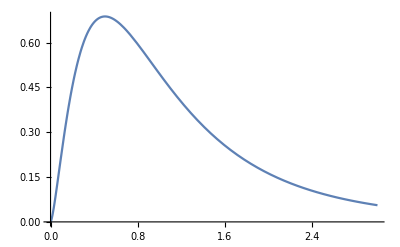

```mathematica
Plot[PDF[FRatioDistribution[5,10],x],{x,0,3}]
```

### Применение и интерпретация

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["genetherapy.csv","Dataset",HeaderLines->1];
dataGen=(data[GroupBy[Last]][[All,All,1]]);
dataGen[All,<|"N"->Length,"M"->Mean,"SD"->StandardDeviation|>]
```

H_0: μ_1=μ_2=μ_3=μ_4

Применим ANOVA:

```mathematica
<<ANOVA`;
ANOVA/.ANOVA[(({Part[#,2],Part[#,1]}&/@Normal@data)/.{"A"->1,"B"->2,"C"->3,"D"->4})]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Model | 3 | 560.717 | 186.906 | 8.0373 | 0.000152497
Error | 56 | 1302.27 | 23.2548 |  | 
Total | 59 | 1862.98 |  |  |

Здесь SumOfSq то же самое, что и SSB. MeanSq - SSB/DF. Как видим по результатам PValue - нулевая гипотеза отклоняется (хотя бы 2 средних отличаются между собой). Теперь посмотрим график:

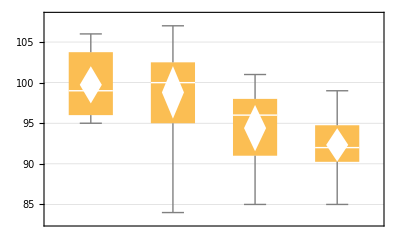

```mathematica
BoxWhiskerChart[Values@Normal@dataGen,{{"MeanDiamond"},{"Outliers"}},PlotTheme->"Detailed"]
```

## Множественные сравнения в ANOVA

### Проблема множественного сравнения выборок

Проблема множественного сравнения возникает когда нужно сравнить множество выборок между собой. Почему при этом нельзя попарно использовать критерий Стьюдента? Для этого приводим пример:

Пусть есть генеральная совокупность со средним 0 и стандартным отклонением 1.

```mathematica
men=0;
dev=1;
```

Из этой совокупности мы будем многократно извлекать выборки и сравнивать их между собой. Функция для изъятия выборок имеет следующий вид:

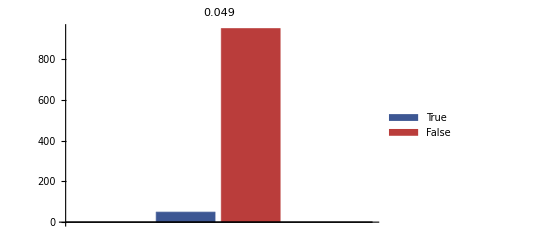

```mathematica
falseAlarm[m_,n_,a_]:=Module[
{trys=1000,dt},
dt=Count[#,True]&@(ContainsAny[#,{True}]&/@Parallelize@Table[(Quiet[TTest[#]<=a]&/@Subsets[Table[RandomVariate[NormalDistribution[men,dev],n],m],{2}]),trys]);
BarChart[{dt,trys-dt},PlotLabel->N@(dt/trys),ChartLegends->{True,False},ChartStyle->"DarkRainbow"]
];
falseAlarm[2,30,0.05]
```

На графике показано в каком проценте случаев мы получили статистически значимые различия. В 5% случаев мы получили статистически значимые различия из одной выборки. То есть на самом деле никаких статистически значимых различий мы не должны были получить. Но поскольку мы выбрали некоторый порог p-уровня значимости после которого мы принимаем различия достоверными. Теперь увеличим количество выборок:

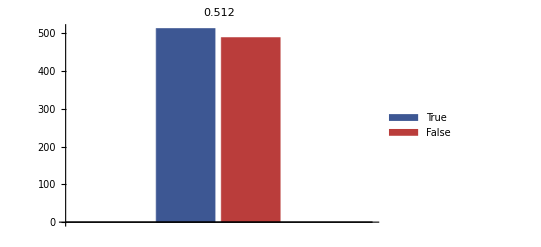

```mathematica
falseAlarm[8, 30, 0.05]
```

Теперь уже в 52% случаев мы получим хотя бы одно статистически значимое различие между 8 выборками несмотря на то, что они из одной генеральной совокупности. Теперь посмотрим что будет если бы сделаем сравнение в 20 выборках:

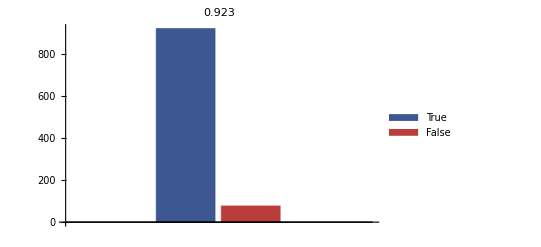

```mathematica
falseAlarm[20,30,0.05]
```

Когда мы сравниваем между собой 2 группы мы принимаем различия значимыми если показатель p меньше 0.05. То есть даже если различий на самом деле нет, в 5% случаев мы бы получили различия случайно. Но когда мы сравниваем 4 комбинации оказывается, что вероятность получить одно различие уже значительно больше. Если мы увеличим количество групп, то вероятность получить различия будет стремиться к единице. Это означает, что если мы многократно увеличиваем количество сравниваемых групп, то вероятность получить хотя бы одно различие, которого на самом деле вообще не существует очень сильнол увеличивается. Таким образом нам нужно корректировать выбор p-уровня. Такой поправкой является поправка Бонферрони.

### Поправка Бонферрони

Если вероятность ошибки первого рода (получить различия там где их нет) возрастает пропорционально количеству групп, которые мы сравниваем, то и показатель α надо так же корректировать. Если мы хотим удержать уровень 0.05, то надо просто поделить его на количество сравнений, которое будет проводиться в эксперименте:

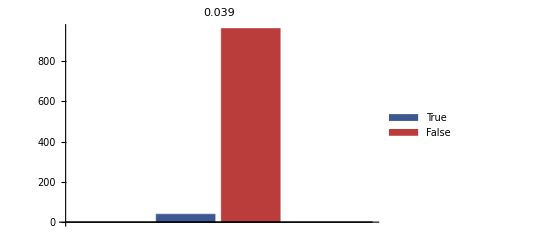

```mathematica
falseAlarm[8,30,0.05/28]
```

Мы вернулись к тому же уровню, что и при 2 сравнениях. Аналогичная ситуация будет и при 20 группах:

```mathematica
(*Ищем количество сравнений*)
Length@Subsets[Table[i,{i,20}],{2}]
```

190

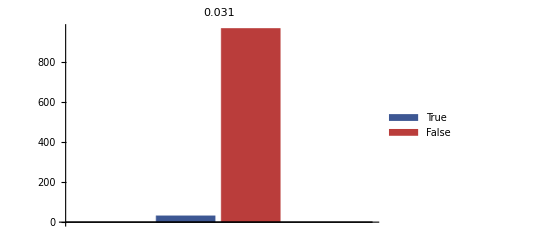

```mathematica
falseAlarm[20, 30, 0.05/190]
```

При достаточном уровне терпения можно всегда получить значимые различия. Допустим мы не смогли отвергнуть нулевую гипотезу и стали добавлять большое число других факторов (пол, место рождения, возраст, семейное положение и тд) и продолжали сравнивать испытуемых по уровню экспрессии гена и на определенном этапе получим значимую связь у испытуемых по месту рождения и сделать выводы о влиянии внешней среды. Проблема в том, что при поправке Бонферрони при 100 сравнениях гарантируется отсутстиве хотя бы одного ложного результата, но при этом упускается около 80% реальных открытий. Поэтому она сильно критикуется: она так понижает уровень значимости, что получить различия зачастую становится невозможным. Но современная статистика вынуждена работать с большим количеством сравнений. Поэтому разработана серия методов, которые работают лучше и возволяет не так сильно понижать p-уровень.

### Критерий Тьюки

Возвращаемся к примеру со сравнением 4х типов терапии. Критерий Тьюки очень похож на TTest, однако инчае рассчитывается стандартная ошибка. С помощью некго можно рассчитать доверительный интервал между средними значениями

OverBar[x_A]- OverBar[x_B]

и если такой доверительный интервал не включает в себя 0, то можно отклонить нулевую гипотезу о равенстве средних.

```mathematica
PostTests/.ANOVA[(({Part[#,2],Part[#,1]}&/@Normal@data)/.{"A"->1,"B"->2,"C"->3,"D"->4}),PostTests->Tukey]
```

{Model→Tukey | {{1,3},{1,4},{2,4}}}

Видим, что значимо отличаются группы A&C, A&D, B&D.

### Интерпретация результатов

Таким образом, если мы сравнили множество групп и не применили поправку, то получаем критику в свой адрес. Если мы применим поправку Бонферрони и остались те же значимые различия, то никаких претензий быть не может. Так же есть более свободные поправки. Более важный вопрос - это зачем вообще производится сравнение. Если мы проверяем какую-то гипотезу и не нашли подтверждений, то можно додавить расчеты так, чтобы что-то там все таки отыскать. Надо так же смотреть на дополнительные факторы. Зачастую значимые различия возникают за счет множественного сравнения, так что нужно применять поправку.

## Многофакторный ANOVA

### Двухфакторный дисперсионный анализ

Начнем с задачи

Атеросклероз довольно опасное заболевание - причина ишемичной болезни сердца и инсультов. Анализ экспрессии генов лейкоцитов позволяет предсказать вероятность развития данного заболевания. В эксперименте исследовался уровень экспрессии в зависимости от возраста пациентов и дозировки лекарства аторвастатина.

```mathematica
dataAth=Import["atherosclerosis.csv","Dataset",HeaderLines->1];
dataAthero=dataAth[GroupBy["age"],GroupBy["dose"]][All,All,All,"expr"][<|"Young"->1,"Old"->2|>][All,<|"High"->"D1","Low"->"D2"|>]
dataAthero[All,All,<|"N"->Length,"Mx"->Mean,"SD"->StandardDeviation|>]
```

Результаты дисперсионного анализа:

```mathematica
twoway=({Part[#,2],Part[#,3],Part[#,1]}&/@(Normal@dataAth))/.{"D1"->1,"D2"->2};
ANOVA/.ANOVA[twoway,{Age,Dose},{Age,Dose}]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Age | 1 | 197.453 | 197.453 | 7.56959 | 0.0078044
Dose | 1 | 16.9122 | 16.9122 | 0.648351 | 0.42383
Error | 61 | 1591.18 | 26.085 |  | 
Total | 63 | 1805.55 |  |  |

Теперь строим график и интерпретируем результат:

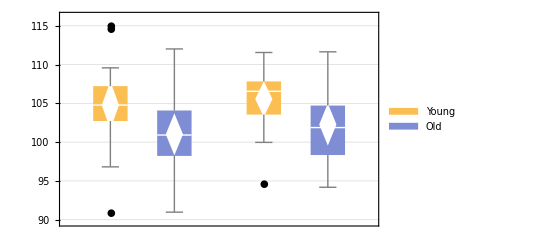

```mathematica
BoxWhiskerChart[Values@Normal@Values@Normal@dataAtheroᵀ,{{"MeanDiamond"},{"Outliers"}},PlotTheme->"Detailed",ChartLegends->{"Young","Old"}]
```

Значимым является только фактор возраста (обращаем внимание, что в ANOVA p-уровень ниже 0.05 только у группы по возрасту) потому что вне зависмости от дозировки, молодые участники оказались с более высоким фактором переменной чем пожилые. Таким образом препарат значимый для фактора возраста, но не значимый для фактора дозировки. Возможна ситуация, когда значимы оба фактора.

### Взаимодействие факторов в ANOVA

Чтобы познакомиться с взаимодействием факторов рассмотрим еще один пример:

Исследователей интересовало влияние инъекции некоторого гормона на показатель концентрации кальция в плазме крови у птиц с учетом их пола. В таблице представлены данные экспериментальной и контрольной группы.

```mathematica
SetDirectory[NotebookDirectory[]];
dataBirds=Import["birds.csv","Dataset",HeaderLines->1];
dataBirdsStats=dataBirds[GroupBy["hormone"],GroupBy["sex"]][All,All,All,"var4"];
dataBirdsStats[All,All,<|"N"->Length,"Mx"->Mean,"SD"->StandardDeviation|>]
```

Результаты дисперсионного анализа:

```mathematica
<<ANOVA`;
twoway=({Part[#,2],Part[#,3],Part[#,1]}&/@(Normal@dataBirds));
ANOVA/.ANOVA[twoway,{Hormone,Sex,All},{Hormone,Sex}]
```

| DF | SumOfSq | MeanSq | FRatio | PValue
Hormone | 1 | 0.847472 | 0.847472 | 0.0865281 | 0.769653
Sex | 1 | 0.119762 | 0.119762 | 0.0122279 | 0.912318
Hormone Sex | 1 | 89.4834 | 89.4834 | 9.13639 | 0.00368175
Error | 60 | 587.65 | 9.79417 |  | 
Total | 63 | 678.101 |  |  |

Мы видим, что ни фактор инъекции, ни фактор пола не оказали значимого влияния на зависимую переменную. Изменчивость их невелика. Взаимодействие оказало значительное влияние. Если мы построим график наших результатов, то увидим следующую картину:

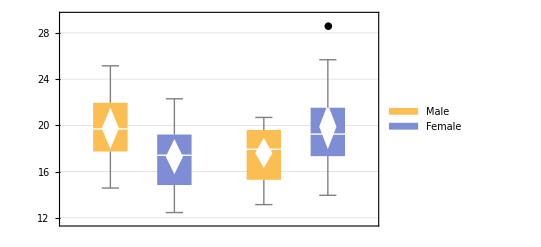

```mathematica
BoxWhiskerChart[Values@Normal@dataBirdsStatsᵀ,{{"MeanDiamond"},{"Outliers"}},PlotTheme->"Detailed",ChartLegends->{"Male","Female"}]
```

Сам факт инъекции по разному повлиял на концентрацию кальция в плазме в зависимости от пола. В случае мужского пола это привело к увеличению интересующего нас показателя и к снижению концентрации в случае женского пола. В этом и заключается идея взаимодействия факторов - когда некоторые переменные оказывают различное влияние на интересующий нас показатель в зависимости от уровней или градации другой независимой переменной.

### Требования к данным

Также важно отметить некоторые требования к данным. Дисперсионный анализ требует нормальность распределения в каждой из групп и гомогенность дисперсий - то есть требование, чтобы дисперсия была примерно одинкаовой в каждой из групп. Приятный факт, что ANOVA достаточно устойчива к обоим этим нарушениям. Но если наблюдений меньше 30 в каждой из групп лучше проверять данные на нормальность распределения и на гомогенность дисперсии. Для проверки гомогенности можно построить BoxPlot и убедиться в отсутствии большого числа выбросов или применить тест Левена и если дисперсии равны, то все хорошо.

### Интерпретация результатов

Само по себе применение дисперсионного анализа не дает оснований говорить о причинной зависимости данных. Например, если мы решим выяснить кто лучше разбирается в статистике - математики, филологи или психологи, и для этого применим дисперсионный анализ, то значимые различия между группами (например математики будут разбираться лучше всего) может означать как тот факт, что те кто занимается математикой лучше научились статистике и теперь лучше её понимают, так и тот, что те, кто лучше понимает статистику становятся математиками, а не филологами или психологами. Дисперсионный анализ проверяет гипотезу о взаимосвязи номинативной профессии и зависимой переменной (средней успеваемости по статистике). Поэтому всегда важно задаваться вопросом “а можно ли объяснить данные с другой стороны”.

## АБ тесты и статистика

Мы подробно изучили теоретические аспекты статистических методов. Пришло время узнать, как статистика применяется на практике для реальных исследований и экспериментов. 
АБ тестирование - это проведение экспериментов при помощи статистики, пожалуй, самый яркий пример того, зачем статистика нужна в реальной жизни!) A/B тесты - один из основных инструментов в продуктовой аналитике. Этот метод маркетингового исследования заключается в том, что контрольная группа элементов сравнивается с набором тестовых групп, где один или несколько показателей изменены для того, чтобы выяснить, какие из изменений улучшают целевой показатель. Например, мы можем поменять цвет кнопки для регистрации с красного на синий и сравнить, насколько это будет эффективно.

Данный раздел предлагается к просмотру на YouTube: https://www.youtube.com/watch?v=gljfGAkgX_o

Корреляция и регрессия

## Понятие корреляции

Начнем знакомствос таким понятием, как корреляция. При помощи корреляции мы научимся исследовать взаимосвязь двух количественных переменных, узнаем что такое положительная и отрицательная корреляции, разберемся как найти коэффициент корреляции и о чем он нам говорит.

Рассмотрим несколько примеров.

Предположим мы захотели узнать как взаимосвязан возраст и физическая активность. Набрали выборку испытуемых и у каждого испытуемого узнали его возраст и число тренировок в неделю. Если нанести все точки на график, то легко заметить, что все значения числа тренировок с ростом возраста будут понижаться.

-Graphics-

Такая взаиомвязь называется отрицательной корреляцией. Если с ростом одной переменной растет и вторая, то такая корреляция называется положительной. Приведенный здесь график называется лиаграмма рассеивания - scatterplot (\[MathematicaIcon]: ListPlot).

По диаграмме рассеивания мы можем понять насколько сильно взаимосвязаны наши переменные, однако нужно что-то более конкретное, показатель. Он называется коэффициентом корреляции.

Найдем формулу для расчета. Для этого используем пример увеличения роста с увеличением веса. Рост обозначим за y, вес за x. График выглядит следующим образом:

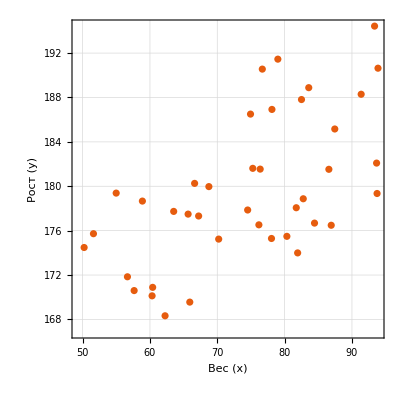

```mathematica
weight=RandomReal[{50,95},40];
height=0.4weight+RandomReal[{-10,10},40]+150;
ListPlot[{weight,height}ᵀ,FrameLabel->{"Вес (x)","Рост (y)"},PlotTheme->"Scientific",GridLines->Automatic,AspectRatio->1]
```

Добавим на график две линии: красная вертикальная будет соответствовать среднем значению веса, а синяя горизонтальная - среднему значению роста.

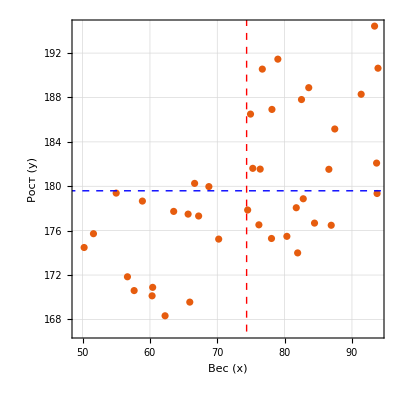

```mathematica
lineW=Line[{{Mean@weight,0},{Mean@weight,200}}];
lineH=Line[{{0,Mean@height},{100,Mean@height}}];
ListPlot[{weight, height}ᵀ, FrameLabel -> {"Вес (x)", "Рост (y)"}, PlotTheme -> "Scientific", GridLines -> Automatic,AspectRatio->1,Epilog->{Directive[{Thick,Red,Dashed}],lineW,Directive[{Thick,Blue,Dashed}],lineH}]
```

Видим, что вся диаграмма разбилась линиями на 4 сектора. Если большая часть наших наблюдений находится в верхнем правом и в нижнем левом секторах, значит наща корреляция положительная, поскольку если человек находится в верхнем правом секторе, то он и тяжелее и выше среднего. Аналогичная ситуация со втором секторе. Теперь для каждой точки рассчитаем следующий параметр:

(x_i-X̄)·(y_i-Ȳ)

Так как отклонение для точек в верхнем правом секторе положительное, то и показатель будет положительный. Для точек в нижнем левом отклонения отрицательные, значит и показатель будет положительным. Для точек из остальных секторов показатели будут отрицательными. Большая часть показателей для точек будет положительной. Теперь сложим все такие показатели и усредним (добавляем -1 в знаменатель, это связано с числом степеней свободы):

(∑(x_i-X̄)·(y_i-Ȳ))/(N-1)

```mathematica
(Total@((weight-Mean@weight)*(height-Mean@height)))/(Length@weight-1)
```

49.7358

Такой показатель называется ковариацией.

```mathematica
Covariance[weight,height]
```

49.7358

Таким образом мы расчитали количественный показатель силы и направления взаимосвязи двух переменных. Чем больше значение ковариации, тем сильнее взаимосвязь и если она положительная, то и корреляция положительная.

Теперь введем именно показатель корреляции:

r_(x y)=cov/(σ_x σ_y)

Таким образом все значения показателя корреляции всегда лежат в интервале [-1; 1].

```mathematica
Covariance[weight,height]/(StandardDeviation[weight]*StandardDeviation[height])
```

0.605754

или

```mathematica
Correlation[weight,height]
```

0.605754

Теперь укажем более традиционную формулу для корреляции (его так же называют коэффициентом корреляции Пирсона):

r_(x y)=cov/(σ_x σ_y)=(∑(x_i-X̄)·(y_i-Ȳ))/((N-1)σ_x σ_y)=(∑(x_i-X̄)·(y_i-Ȳ))/((N-1)√((∑(x_i-X̄)^2)/(N-1))√((∑(y_i-Ȳ)^2)/(N-1)))=

=(∑(x_i-X̄)·(y_i-Ȳ))/((N-1)·1/(N-1)√(∑(x_i-X̄)^2)√(∑(y_i-Ȳ)^2))=(∑(x_i-X̄)·(y_i-Ȳ))/(√(∑(x_i-X̄)^2)√(∑(y_i-Ȳ)^2))=

=(∑(x_i-X̄)·(y_i-Ȳ))/(√(∑(x_i-X̄)^2∑(y_i-Ȳ)^2))

Квадрат коэффициента корреляции называется коэффициентом детерминации и показывает, в какой степени дисперсия одной переменной обусловлена влиянием другой переменной. Принимает значения [0,1].

Теперь перейдем к вопросу, как проверять статистические гипотезы используя коэффициент корреляции Пирсона. возвращаемся к примеру с ростом и весом.

Сформулируем нулевую гипотезу: r_(x y)=0. Альтернативная гипотеза говорит: r_(x y)!= 0. В нашем эксперименте мы получили определенную связь между ростом и весом. Теперь надо найти p-уровень значимости для гипотезы. Мы будем расчитывать t-критерий при числе степеней свободы N-2 (на вопрос почему ответим позже в разделе про линейную регрессию).

Еще один пример:

Чему равен коэффициент корреляции в данной выборке

x | y
4 | 2
5 | 1
2 | 4
3 | 3
1 | 5

Решение:

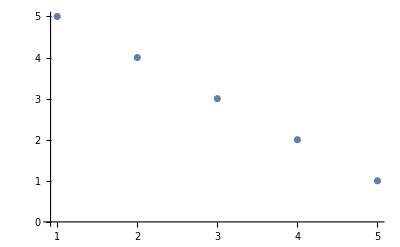

-1

```mathematica
x={4,5,2,3,1};
y={2,1,4,3,5};
ListPlot[{x,y}ᵀ]
Correlation[x,y]
```

## Условия приенения коэффициента корреляции

Завершая разговор о корреляциях остановимся на нескольких важных моментах, посвященных правильной интерпретации получаемых данных в корреляционных исследованиях.

Первая из них - ошибка корреляции. Её суть заключается в том, что положительная или отрицательная взаимосвязь еще не обязательно говорит о причинно-следственной зависимости. Допустим мы решили выяснить, действительно ли компьютерные игры негативно влияют на подростков (агрессивное поведение). Взяли 500 школьников и посмотрели как часто они дерутся со сверстниками и как часто они играют в игры. Если мы получили значимую положительную корреляцию, это еще не значит, что именно игры стали причиной агрессивного поведения. Возможно это агрессивные школьники любят играть в компьютерные игры.

Сама по себе корреляция не означает наличие причинно-следственной зависимости, но может её означать. Корреляция может подтверждать выдвинутую теорию.

Второй момент - это влияние так называемой третьей переменной. Это такая неявная перменная, которая не входит в рассмотрение, но именно она является причиной корреляции. Например: размер ноги школьника хорошо коррелирует со знаниями математики. Потому что чем он старше, тем у него и размер ноги больше, и знаний больше.

## Регрессия с одной независимой перменной

В этом и следующих уроках мы научимся работать  с одномерным регрессионным анализом, который позволяет проверять гипотезы о взаимосвязи одной  количественной зависимой переменной и нескольких независимых.
Сначала мы познакомимся с самым простым вариантом -  простой линейной регрессией, при помощи которой можно исследовать взаимосвязь двух переменных. Затем перейдем к множественной регрессии с несколькими независимыми переменными.

Регрессионный анализ это набор методов, позволяющих исследовать взаимосвязь различных переменных между собой. Начнем мы с простой линейной регрессии, которая как и коэффициент корреляции позволяет нам исследовать взаимосвязь двух количественных переменных. Однако позволяет делать это более интересным образом.

### Линия регрессии

Одномерный регрессионный анализ применяется для исследования взаимосвязи двух переменных. Пусть в нашем случае это буду x и y. Переменная по оси y называется зависимая переменная, а x - это независимая переменная или предиктор.

Регрессионный анализ обычно применяется, чтобы посмотреть как одна переменная объясняет другую переменную. Например, хотим посмотреть как на качество товара влияет его цена. Если две переменные как-то взаимосвязаны между собой удобно добавить линию на диаграмму. Нам нужно, чтобы она следовала за облаком точек на диаграмме и чтобы она хорошо описывала распределение данных.

Мы знаем, что любая линия задается двумя параметрами:

y=b_0+b_1 x

здесь, b_0(intercept) отвечает за точку пересечения линии с осью Y, а b_1(slope) за наклон линии. Один из самых простых методов построения такой прямой это метод наименьших квадратов.

### Метод наименьших квадратов

МНК - метод нахождения оптимальных параметров линейной регресии, таких, что сумма квадратов ошибок (остатков) была минимальна.

Остаток, это расстояние от отдельно выбранной точки до прямой. Оно рассчитывается как:

e_i=y_i-OverHat[y_i]

Сложением квадратов мы избегаем зануление одинаково отстоящих точек. Расчет:

b_1=sd_y/sd_x r_(x y), b_0=ȳ-b_1 x̄

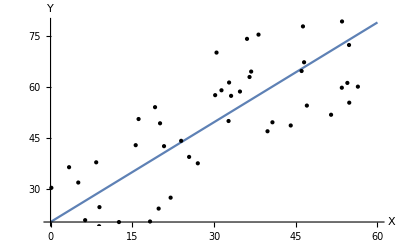

```mathematica
dataX=RandomReal[{0,60},50];
dataY=dataX+RandomReal[{0,40},50];
fit=LinearModelFit[{dataX,dataY}ᵀ,x,x];
Plot[fit[x],{x,0,60},Epilog->Point[{dataX,dataY}ᵀ],AxesLabel->{X,Y}]
```

#### Задача

На графике изображена зависимость двух количественных переменных X и Y. Рассчитайте коэффициент b_1 для регрессионной прямой, если коэффициент детерминации равен 0.25:

M_x=15 (выборочное среднее)

D_x=25

M_y=10

D_y=36

Формула для b_1: b_1=sd_y/sd_x r_(x y). sd=√D, коэффициент детерминации: (r_(x y))^2. Итого:

```mathematica
(√36)/(√25)√0.25
```

0.6

## Гипотеза о значимости взаимосвязи и коэффициент детерминации

Теперь когда мы построили линию регрессии мы хотим ответить на вопрос “на сколько статстически значима взаимосвязь двух наших переменных”. За взаимосвязь отвечает именно b_1. Если коэффициент корреляции 0, то прямая проходит параллельно оси X. Таким образом, если переменные не связаны между собой, то b_1 становися равен 0.

То есть появляются две гипотезы:

H_0: b_1=0

H_1: b_1!=0

Теперь появляется t-критерий, который говорит, что если бы мы многократно повторяли эксперимент и данные на самом деле не зависят, то выборочные значения коэффициентов b_1 распределились бы нормально относительно 0 и отклонялись бы то в правую, то в левую сторону. Теперь можно расчитать t-критерий который будет сообщать насколько выборочное b_1 отклонится от ожидаемого. И здесь он будет соответствовать формуле: t=b_1/se.

### Коэффициент детермнации

Одномерный дисперсионный анализ позволяет нам построить некоторую модель взаимосвязи двух количественных переменных, проверить гипотезу о наличии взаимосвязи, рассчитав соответствующий p-уровень значимости и получить значение коэффициента детерминации (R^2).